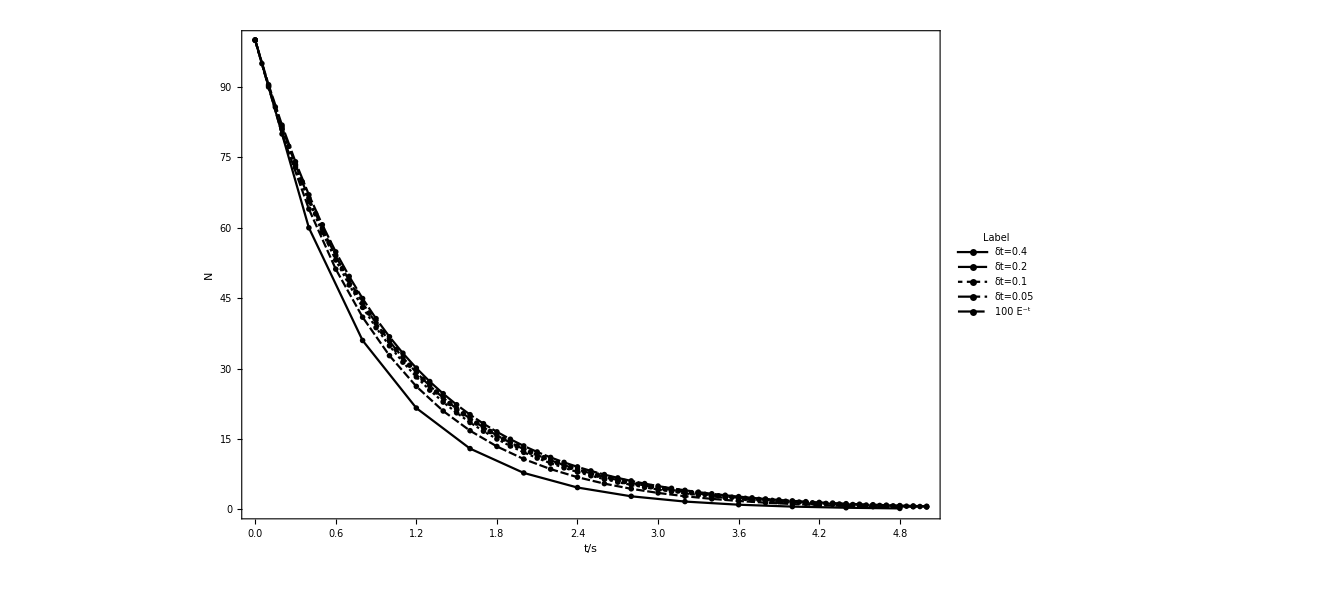

```mathematica
list1=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.2\\python\\output0.4.txt","list"];list2=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.2\\python\\output0.2.txt","list"];list3=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.2\\python\\output0.1.txt","list"];list4=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.2\\python\\output0.05.txt","list"];list={list1,list2,list3,list4};ListPlot[Table[Table[{list[[j,i]]//ToExpression,list[[j,i+1]]//ToExpression},{i,1,Length[list[[j]]],2}] ,{j,1,4}]//Append[Table[{t,100 E^-t},{t,0,5,0.1}]],Joined->True,PlotTheme->"Monochrome",Frame->True,PlotLegends->Placed[LineLegend[{"δt=0.4","δt=0.2","δt=0.1","δt=0.05","100 E^-t"},LegendLabel->"Label",LegendFunction->(Framed[#,Background->LightBlue]&)],{0.8,0.7}],FrameLabel->{"t/s","N"},LabelStyle->{Bold, Medium}]
```